## Canales cuánticos

```mathematica
Style[Graphics3D[{
{RGBColor["#13BD00"],Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,-(√3)/2,1/2}},0.025]]},
(*{Black,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,-1,0}},0.01]]},*){Red,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{1,0,0}},0.025]]},(*{Red,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{-1,0,0}},0.01]]},*){Blue,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,1/2,(√3)/2}},0.025]]},
(*{Blue,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,0,-1}},0.01]]},*)(*{Directive[Thickness[10],FontSize->18],Text["0_y",{0,1.2,0}]},*){Directive[FontWeight->Bold,FontSize->18],Text["cos(π/6)0 + ⅈ sin(π/6)1",{0.1,-0.97,0.4}]},
{Directive[FontWeight->Bold,FontSize->18],Text["cos(π/12)0 + ⅈ sin(π/12)1",{0,0.6,0.9}]},{Directive[FontWeight->Bold,FontSize->18],Text["(0 +1)/(√2)",{1,0,-0.5}]},
Orange,Specularity[White,2],Opacity[0.3],Sphere[{0,0,0}]},Axes->True,AxesLabel->{"x","y","z"},Ticks->None,LabelStyle->Directive[ Bold,FontSize->50,Black],BoxStyle->Directive[Bold,Black,Thick]],RenderingOptions->{"3DRenderingMethod"->"HardwareDepthPeeling"}
]
```

-Graphics3D-

```mathematica
Style[Graphics3D[{
{RGBColor["#13BD00"],Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,0,1}},0.025]]},
(*{Black,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,-1,0}},0.01]]},*){Red,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{1,0,0}},0.025]]},(*{Red,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{-1,0,0}},0.01]]},*){Blue,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,1,0}},0.025]]},
(*{Blue,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,0,-1}},0.01]]},*)(*{Directive[Thickness[10],FontSize->18],Text["0_y",{0,1.2,0}]},*){Directive[FontWeight->Bold,FontSize->18],Text["0",{0,0,1.1}]},
{Directive[FontWeight->Bold,FontSize->18],Text["(0 +ⅈ 1)/(√2)",{.15,1.1,0.1}]},{Directive[FontWeight->Bold,FontSize->18],Text["(0 +1)/(√2)",{1,0,-0.5}]},
Orange,Specularity[White,2],Opacity[0.3],Sphere[{0,0,0}]},Axes->True,AxesLabel->{"x","y","z"},Ticks->None,LabelStyle->Directive[ Bold,FontSize->50,Black],BoxStyle->Directive[Bold,Black,Thick]],RenderingOptions->{"3DRenderingMethod"->"HardwareDepthPeeling"}
]
```

-Graphics3D-

```mathematica
.b4
```

```mathematica
Style[Graphics3D[{{Black,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,0,1}},0.01]]},{Red,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{1,0,0}},0.01]]},{Blue,Arrowheads[0.06],Arrow[Tube[{{0,0,0},{0,-1,0}},0.01]]},Opacity[0.35],Sphere[{0,0,0}]},Axes->True,AxesLabel->{"x","y","z"},Ticks->None,LabelStyle->Directive[ Bold,Large,Black],BoxStyle->Directive[Bold,Black,Thick]],RenderingOptions->{"3DRenderingMethod"->"HardwareDepthPeeling"}
]
```

-Graphics3D-

```mathematica
Graphics3D[Ellipsoid[{0,0,0},{1,1,1}],PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y","z"},Ticks->None,LabelStyle->Directive[ Bold,FontSize->50,Black],BoxStyle->Directive[Bold,Black,Thick]]
```

-Graphics3D-

```mathematica
Graphics3D[{Orange,Thickness[0.025],Line[{{0,-1,0},{0,1,0}}]},PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y","z"},Ticks->None,LabelStyle->Directive[ Bold,FontSize->50,Black],BoxStyle->Directive[Bold,Black,Thick]]
```

-Graphics3D-

```mathematica
2.35/2.55
```

0.921569

```mathematica
2.35/(2.93/3.18)
```

2.55051

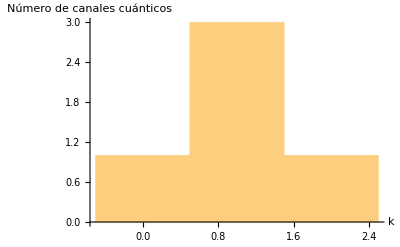

```mathematica
Histogram[{0,1,1,1,2},AxesLabel->{Style[k,Large,Bold],Style["Número\nde canales\n cuánticos",Large,Bold]}]
```

```mathematica
Export["Documents/requisitos-lic/tesis/informe-tesis/img/presentacion/mirroring_1qubits.pdf",Labeled[Histogram[{0,1,1,1,2},Ticks->{{0,1,2},{0,1,2,3}},TicksStyle->Directive[Black,Bold,25]],{Style["Número de\ncanales PCE",FontSize->25,Bold],Style[k,FontSize->25,Bold]},{Left,Bottom},RotateLabel->True]]
```

Documents/requisitos-lic/tesis/informe-tesis/img/presentacion/mirroring_1qubits.pdf

```mathematica
Export["Documents/requisitos-lic/tesis/informe-tesis/img/presentacion/mirroring_2qubits.pdf",Labeled[Histogram[Join[{0},ConstantArray[1,15],ConstantArray[2,35],ConstantArray[3,15],{4}],Ticks->{{0,1,2,3,4},{0,15,35}},TicksStyle->Directive[Black,Bold,25]],{Style["Número de\ncanales PCE",FontSize->25,Bold],Style[k,FontSize->25,Bold]},{Left,Bottom},RotateLabel->True]]
```

Documents/requisitos-lic/tesis/informe-tesis/img/presentacion/mirroring_2qubits.pdf

```mathematica
Export["Documents/requisitos-lic/tesis/informe-tesis/img/presentacion/mirroring_3qubits.pdf",
Labeled[Histogram[{Join[{0},ConstantArray[1,63],ConstantArray[2,651],{6}],Join[ConstantArray[4,651],ConstantArray[5,63]]},Ticks->{{0,1,2,3,4,5,6},{0,63,651}},TicksStyle->Directive[Black,Bold,25]],{Style["Número de\ncanales PCE",FontSize->25,Bold],Style[k,FontSize->25,Bold]},{Left,Bottom},RotateLabel->True]]
```

Documents/requisitos-lic/tesis/informe-tesis/img/presentacion/mirroring_3qubits.pdf